For directivity approximation:

```mathematica
ClearAll[p]
Cos[p -Pi/4]^2 - Cos[p + Pi/4]^2 // TrigExpand 
(*Plot[Cos[p -Pi/4]^2 + Cos[p + Pi/4]^2, {p, 0, 2 Pi}]*)

Integrate[ Sin[2p]^2, {p, 0, Pi/2}]
Integrate[ Sin[t]^7, {t, 0, Pi}]
2 Pi Integrate[ Sin[t]^3, {t, 0, Pi}]

35/2 / (3/2) // N
```

2 Cos[p] Sin[p]

π/4

32/35

(8 π)/3

11.6667

```mathematica
2 Cos[p] Sin[p] // TrigReduce
```

Sin[2 p]

Part (d).  Plots of |AF|^2 in XY plane.

```mathematica
ClearAll[aa, xx, af, pp]
af[a_,t_, p_] = 2 Cos[ 2 Pi a Sin[t]Cos[p - Pi/4] ] - 2 Cos[ 2 Pi a Sin[t] Cos[p + Pi/4]] ;
pp = Plot3D[ af[a,Pi/2, p], {a, 0, 1.5}, {p, 0, 2 Pi}, AxesLabel -> {α, ϕ}]
```

-Graphics3D-

```mathematica
<<peeters` ;
peeters`setGitDir[ "figures\\ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

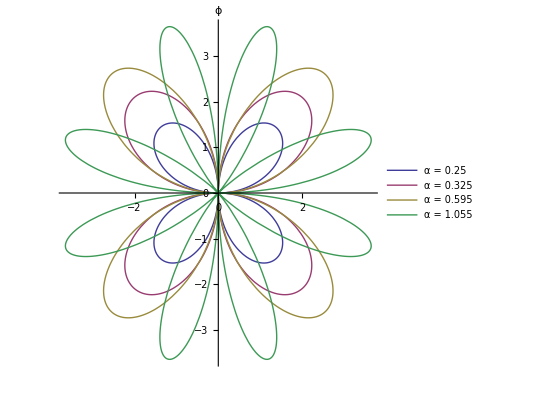

```mathematica
(*TrigExpand[Sqrt[2]Cos[p+Pi/4]]
TrigExpand[Sqrt[2]Cos[p-Pi/4]]*)
(*aa = {0.5} ; *)
aa = {0.25,0.325,0.595,1.055} ;

(* aa = {0.1, 0.25, 0.5} ;*)
xx = PolarPlot[af[#, Pi/2, p] &/@ aa // Evaluate, {p, 0, 2 Pi}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"α = ", #}]&/@aa, {Right,Bottom}]]
```

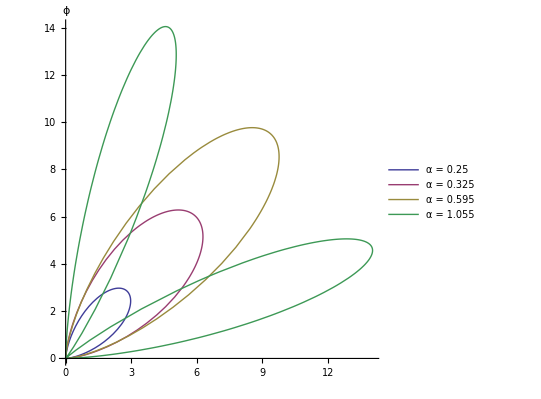

```mathematica
bb = Table[i/10, {i, 10}] ;
bb = aa ;
yy = PolarPlot[af[#, Pi/2, p]^2 &/@ bb // Evaluate, {p, 0, Pi/2}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"α = ", #}]&/@bb, {Right,Bottom}]]
```

```mathematica
Manipulate[ PolarPlot[af[a, Pi/2, p]^2,{p, 0, Pi/2}, AxesLabel -> ϕ ],
{{a,0.25,"s/λ"}, 0, 3, Appearance->"Labeled"}]
```

```mathematica
peeters`exportForLatex["arrayFactorXYCorrectedFig4", pp]
peeters`exportForLatex["arrayFactorXYCorrectedFig5", xx]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYCorrectedFig4.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYCorrectedFig4pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYCorrectedFig5.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYCorrectedFig5pn.png}

```mathematica
peeters`exportForLatex["arrayFactorXYSqCorrectedFig5", yy]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYSqCorrectedFig5.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYSqCorrectedFig5pn.png}

Part (e).  Numerical calculations of the directivity.

```mathematica
ClearAll[Uccube, dir, aa, Umax, Prad]
Uccube[a_, p_, t_] =  Sin[t]^2 af[a, p, t]^2 ;
Umax[a_] := 
NMaximize[{Uccube[a, p, t], 0 ≤ p ≤ Pi/2,  0 ≤ t ≤ Pi},{p, t}] ;
Prad[a_] := NIntegrate[Uccube[a, p, t], {p, 0, Pi/2}, {t, 0, Pi}]  ;
dir[a_] := 4 Pi Umax[a][[1]]/Prad[a]  ;
aa = {1/8, 1/4, 1/2} ;

dir[#]&/@ {1/8, 1/4, 1/2}
```

{5.93207,9.07849,18.3207}

```mathematica
Manipulate[ 

Show[
ParametricPlot3D[ 
{af[a, t, p]^2 rcap[t, p]},
 {t, 0, Pi}, 
{p, 0, Pi/2}, 
AxesLabel -> {x, y, z},
PlotRange -> {{0,range},{0,range},{-range, range}},
PlotStyle->Directive[Opacity[0.6]],
ViewPoint ->{2.616433634989163,1.0060144996548517,1.89531260223257}
,PerformanceGoal->pg
]
,axes
] 


, {{range, 18}, 1, 25}
,{{a,0.25,"s/λ"}, 0, 3, Appearance->"Labeled"}
, {{pg, "Quality", "Plot Rendering"}, {"Quality", "Speed"}}
,Initialization:> {

rcap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
(*phicap = {-Sin[#2], Cos[#2], 0} & ;
thetacap = {Cos[#1] Cos[#2], Cos[#1] Sin[#2], -Sin[#1]} & ;*)


asz = 1.5 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;
}
(*,SaveDefinitions->True*)
]
```

```mathematica
zz = With[{a=0.6900000000000001,pg="Quality",range=18},Show[ParametricPlot3D[{af[a,t,p]^2 rcap[t,p]},{t,0,π},{p,0,π/2},AxesLabel->{x,y,z},PlotRange->{{0,range},{0,range},{-range,range}},PlotStyle->Directive[Opacity[0.6]],ViewPoint->{2.616433634989163,1.0060144996548517,1.89531260223257},PerformanceGoal->pg],axes]]
```

-Graphics3D-

```mathematica
peeters`exportForLatex["arrayFactorXYSqIn3DFig6", zz]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYSqIn3DFig6.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYSqIn3DFig6pn.png}